## Select some nodes that are equivalent to B43, B44, B...

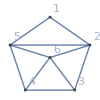
-Graphics-{B43→v13x24x5+v14x2x35+2 v1x24x35+v1x24x3x5+v1x2x35x4,6}Would be inconsistent with other inequalities

```mathematica
CosyPrint5["B43",treeForm5]
```

```mathematica
b43InBase6=First[Select[Keys[stubbornForm6],With[{g=stubbornForm6[#,"graph"]},VertexCount[g]==6&&EdgeCount[g]==10&&EdgeQ[g,1<->2]&&EdgeQ[g,2<->3]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,5<->1]
&&EdgeQ[g,2<->5]
&&EdgeQ[g,2<->6]&&EdgeQ[g,3<->6]&&EdgeQ[g,4<->6]&&EdgeQ[g,5<->6]
]&]]
```

4982998

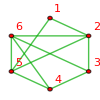
-Graphics-{4982998→v13x24x5x6+v13x2x4x5x6+v14x2x35x6+v14x2x3x5x6+v16x24x35+v16x24x3x5+v16x2x35x4+v16x2x3x4x5+v1x24x35x6+v1x24x3x5x6+v1x2x35x4x6+v1x2x3x4x5x6,6}Missing[KeyAbsent,compwhy]

```mathematica
CosyPrint6[b43InBase6,stubbornForm6]
```

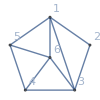
-Graphics-{B44→v14x25x3+2 v14x2x35+v14x2x3x5+v1x24x35+v1x2x35x4,6}Would be inconsistent with other inequalities

```mathematica
CosyPrint5["B44",treeForm5]
```

```mathematica
b44InBase6=First[Select[Keys[stubbornForm6],With[{g=stubbornForm6[#,"graph"]},VertexCount[g]==6&&EdgeCount[g]==10&&EdgeQ[g,1<->2]&&EdgeQ[g,2<->3]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,5<->1]
&&EdgeQ[g,1<->3]
&&EdgeQ[g,1<->6]&&EdgeQ[g,3<->6]&&EdgeQ[g,4<->6]&&EdgeQ[g,5<->6]
]&]]
```

6633454

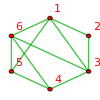
-Graphics-{6633454→v14x25x3x6+v14x26x35+v14x26x3x5+v14x2x35x6+v14x2x3x5x6+v1x24x35x6+v1x24x3x5x6+v1x25x3x4x6+v1x26x35x4+v1x26x3x4x5+v1x2x35x4x6+v1x2x3x4x5x6,6}Missing[KeyAbsent,compwhy]

```mathematica
CosyPrint6[b44InBase6,stubbornForm6]
```

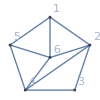
-Graphics-{B45→v13x25x4+2 v14x25x3+v14x2x35+v14x2x3x5+v1x25x3x4,6}Would be inconsistent with other inequalities

```mathematica
CosyPrint5["B45",treeForm5]
```

```mathematica
b45InBase6=First[Select[Keys[stubbornForm6],With[{g=stubbornForm6[#,"graph"]},VertexCount[g]==6&&EdgeCount[g]==10&&EdgeQ[g,1<->2]&&EdgeQ[g,2<->3]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,5<->1]
&&EdgeQ[g,2<->4]
&&EdgeQ[g,1<->6]&&EdgeQ[g,2<->6]&&EdgeQ[g,4<->6]&&EdgeQ[g,5<->6]
]&]]
```

5046394

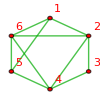
-Graphics-{5046394→v13x25x4x6+v13x2x4x5x6+v14x25x36+v14x25x3x6+v14x2x35x6+v14x2x36x5+v14x2x3x5x6+v1x25x36x4+v1x25x3x4x6+v1x2x35x4x6+v1x2x36x4x5+v1x2x3x4x5x6,6}Missing[KeyAbsent,compwhy]

```mathematica
CosyPrint6[b45InBase6,stubbornForm6]
```

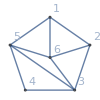
-Graphics-{B46→v13x24x5+2 v13x25x4+v13x2x4x5+v14x25x3+v1x25x3x4,6}Would be inconsistent with other inequalities

```mathematica
CosyPrint5["B46",treeForm5]
```

```mathematica
b46InBase6=First[Select[Keys[stubbornForm6],With[{g=stubbornForm6[#,"graph"]},VertexCount[g]==6&&EdgeCount[g]==10&&EdgeQ[g,1<->2]&&EdgeQ[g,2<->3]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,5<->1]
&&EdgeQ[g,3<->5]
&&EdgeQ[g,1<->6]&&EdgeQ[g,2<->6]&&EdgeQ[g,3<->6]&&EdgeQ[g,5<->6]
]&]]
```

5039938

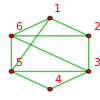
-Graphics-{5039938→v13x24x5x6+v13x25x46+v13x25x4x6+v13x2x46x5+v13x2x4x5x6+v14x25x3x6+v14x2x3x5x6+v1x24x3x5x6+v1x25x3x46+v1x25x3x4x6+v1x2x3x46x5+v1x2x3x4x5x6,6}Missing[KeyAbsent,compwhy]

```mathematica
CosyPrint6[b46InBase6,stubbornForm6]
```

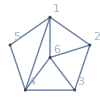
-Graphics-{B47→2 v13x24x5+v13x25x4+v13x2x4x5+v1x24x35+v1x24x3x5,6}Would be inconsistent with other inequalities

```mathematica
CosyPrint5["B47",treeForm5]
```

```mathematica
b47InBase6=First[Select[Keys[stubbornForm6],With[{g=stubbornForm6[#,"graph"]},VertexCount[g]==6&&EdgeCount[g]==10&&EdgeQ[g,1<->2]&&EdgeQ[g,2<->3]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,5<->1]
&&EdgeQ[g,1<->4]
&&EdgeQ[g,1<->6]&&EdgeQ[g,2<->6]&&EdgeQ[g,3<->6]&&EdgeQ[g,4<->6]
]&]]
```

5571300

```mathematica
CosyPrint6[b47InBase6,stubbornForm6]
```

## First we define a replacement for the zeroes in base 6 this that are know to contain K5)

```mathematica
repSixZeroes=Table[stubbornForm6[key,"colofour"]->0,{key,Select[baseKeys6,ToString[stubbornForm6[#,"comp"]]=="Equal"&]}]
```

{v12x3x4x5x6→0,v13x2x4x5x6→0,v14x2x3x5x6→0,v15x2x3x4x6→0,v16x2x3x4x5→0,v1x23x4x5x6→0,v1x24x3x5x6→0,v1x25x3x4x6→0,v1x26x3x4x5→0,v1x2x34x5x6→0,v1x2x35x4x6→0,v1x2x36x4x5→0,v1x2x3x45x6→0,v1x2x3x46x5→0,v1x2x3x4x56→0,v1x2x3x4x5x6→0}

```mathematica
repFiveZeroes=Table[stubbornForm5[key,"colofour"]->0,{key,Select[baseKeys5,ToString[stubbornForm5[#,"comp"]]=="Equal"&]}]
```

{v1x2x3x4x5→0}

## Here are some of the suspects

```mathematica
ColorTablePrint[b46InBase6,stubbornForm6,"colofour","colortable",Join[repSixZeroes,repcolofour6base],600]
```

-Graphics-5039938v13x24x5x6+v13x25x46+v13x25x4x6+v13x2x46x5+v13x2x4x5x6+v14x25x3x6+v14x2x3x5x6+v1x24x3x5x6+v1x25x3x46+v1x25x3x4x6+v1x2x3x46x5+v1x2x3x4x5x6GreaterEqual
( | = | ≠
1<->2 | 0 | -Graphics-v13x25x46+-Graphics-v13x24x5x6+-Graphics-v13x25x4x6+-Graphics-v1x25x3x46+-Graphics-v14x25x3x6+-Graphics-v13x2x46x5
1<->3 | -Graphics-v13x25x46+-Graphics-v13x24x5x6+-Graphics-v13x25x4x6+-Graphics-v13x2x46x5 | -Graphics-v1x25x3x46+-Graphics-v14x25x3x6
1<->4 | -Graphics-v14x25x3x6 | -Graphics-v13x25x46+-Graphics-v13x24x5x6+-Graphics-v13x25x4x6+-Graphics-v1x25x3x46+-Graphics-v13x2x46x5
1<->5 | 0 | -Graphics-v13x25x46+-Graphics-v13x24x5x6+-Graphics-v13x25x4x6+-Graphics-v1x25x3x46+-Graphics-v14x25x3x6+-Graphics-v13x2x46x5
1<->6 | 0 | -Graphics-v13x25x46+-Graphics-v13x24x5x6+-Graphics-v13x25x4x6+-Graphics-v1x25x3x46+-Graphics-v14x25x3x6+-Graphics-v13x2x46x5
2<->3 | 0 | -Graphics-v13x25x46+-Graphics-v13x24x5x6+-Graphics-v13x25x4x6+-Graphics-v1x25x3x46+-Graphics-v14x25x3x6+-Graphics-v13x2x46x5
2<->4 | -Graphics-v13x24x5x6 | -Graphics-v13x25x46+-Graphics-v13x25x4x6+-Graphics-v1x25x3x46+-Graphics-v14x25x3x6+-Graphics-v13x2x46x5
2<->5 | -Graphics-v13x25x46+-Graphics-v13x25x4x6+-Graphics-v1x25x3x46+-Graphics-v14x25x3x6 | -Graphics-v13x24x5x6+-Graphics-v13x2x46x5
2<->6 | 0 | -Graphics-v13x25x46+-Graphics-v13x24x5x6+-Graphics-v13x25x4x6+-Graphics-v1x25x3x46+-Graphics-v14x25x3x6+-Graphics-v13x2x46x5
3<->4 | 0 | -Graphics-v13x25x46+-Graphics-v13x24x5x6+-Graphics-v13x25x4x6+-Graphics-v1x25x3x46+-Graphics-v14x25x3x6+-Graphics-v13x2x46x5
3<->5 | 0 | -Graphics-v13x25x46+-Graphics-v13x24x5x6+-Graphics-v13x25x4x6+-Graphics-v1x25x3x46+-Graphics-v14x25x3x6+-Graphics-v13x2x46x5
3<->6 | 0 | -Graphics-v13x25x46+-Graphics-v13x24x5x6+-Graphics-v13x25x4x6+-Graphics-v1x25x3x46+-Graphics-v14x25x3x6+-Graphics-v13x2x46x5
4<->5 | 0 | -Graphics-v13x25x46+-Graphics-v13x24x5x6+-Graphics-v13x25x4x6+-Graphics-v1x25x3x46+-Graphics-v14x25x3x6+-Graphics-v13x2x46x5
4<->6 | -Graphics-v13x25x46+-Graphics-v1x25x3x46+-Graphics-v13x2x46x5 | -Graphics-v13x24x5x6+-Graphics-v13x25x4x6+-Graphics-v14x25x3x6
5<->6 | 0 | -Graphics-v13x25x46+-Graphics-v13x24x5x6+-Graphics-v13x25x4x6+-Graphics-v1x25x3x46+-Graphics-v14x25x3x6+-Graphics-v13x2x46x5)

## We now define a procedure that can match a graph in base 6 with its equivalent in base 5

```mathematica
GenerateEquationsFiveSix[keyFive_,keySix_,zero_]:=Block[{s,f,indices={5,9,12,14,15} (* indices between "zero" and 6 in base 6*)},
With[
{six=stubbornForm6[keySix,"colortable"]/.repSixZeroes,
five=treeForm5[keyFive,"colortable"]/.repFiveZeroes},
Fold[And,
Table[
{f,s}=k;
six[[s,1]]==five[[f,1]]&&
six[[s,2]]==five[[f,2]]
,
{k,{{1,1},{2,2},{3,3},{4,4},{5,6},{6,7},{7,8},{8,10},{9,11},{10,13}}}
]]&&
stubbornForm6[keySix]["colofour"]==treeForm5[keyFive]["colofour"]
&& six[[indices[[zero]],2]]==0

]
]
```

```mathematica
GenerateEquationsFiveSix["B46",b46InBase6,5]
```

v13x24x5x6+v13x25x46+v13x25x4x6+v13x2x46x5+v14x25x3x6+v1x25x3x46==v13x24x5+2 v13x25x4+v13x2x4x5+v14x25x3+v1x25x3x4&&v13x24x5x6+v13x25x46+v13x25x4x6+v13x2x46x5==v13x24x5+2 v13x25x4+v13x2x4x5&&v14x25x3x6+v1x25x3x46==v14x25x3+v1x25x3x4&&v14x25x3x6==v14x25x3&&v13x24x5x6+v13x25x46+v13x25x4x6+v13x2x46x5+v1x25x3x46==v13x24x5+2 v13x25x4+v13x2x4x5+v1x25x3x4&&v13x24x5x6+v13x25x46+v13x25x4x6+v13x2x46x5+v14x25x3x6+v1x25x3x46==v13x24x5+2 v13x25x4+v13x2x4x5+v14x25x3+v1x25x3x4&&v13x24x5x6+v13x25x46+v13x25x4x6+v13x2x46x5+v14x25x3x6+v1x25x3x46==v13x24x5+2 v13x25x4+v13x2x4x5+v14x25x3+v1x25x3x4&&v13x24x5x6==v13x24x5&&v13x25x46+v13x25x4x6+v13x2x46x5+v14x25x3x6+v1x25x3x46==2 v13x25x4+v13x2x4x5+v14x25x3+v1x25x3x4&&v13x25x46+v13x25x4x6+v14x25x3x6+v1x25x3x46==2 v13x25x4+v14x25x3+v1x25x3x4&&v13x24x5x6+v13x2x46x5==v13x24x5+v13x2x4x5&&v13x24x5x6+v13x25x46+v13x25x4x6+v13x2x46x5+v14x25x3x6+v1x25x3x46==v13x24x5+2 v13x25x4+v13x2x4x5+v14x25x3+v1x25x3x4&&v13x24x5x6+v13x25x46+v13x25x4x6+v13x2x46x5+v14x25x3x6+v1x25x3x46==v13x24x5+2 v13x25x4+v13x2x4x5+v14x25x3+v1x25x3x4&&v13x24x5x6+v13x25x46+v13x25x4x6+v13x2x46x5+v14x25x3x6+v1x25x3x46==v13x24x5+2 v13x25x4+v13x2x4x5+v14x25x3+v1x25x3x4&&v13x24x5x6+v13x25x46+v13x25x4x6+v13x2x46x5+v13x2x4x5x6+v14x25x3x6+v14x2x3x5x6+v1x24x3x5x6+v1x25x3x46+v1x25x3x4x6+v1x2x3x46x5+v1x2x3x4x5x6==v13x24x5+2 v13x25x4+v13x2x4x5+v14x25x3+v1x25x3x4&&v13x24x5x6+v13x25x46+v13x25x4x6+v13x2x46x5+v14x25x3x6+v1x25x3x46==0

Combine all of these
Table[

```mathematica
fiveequalssix=Flatten[
Fold[And,
Block[{f,s,zero},
Table[{f,s,zero}=key;GenerateEquationsFiveSix[f,s,zero],{key,{{"B43",b43InBase6,1},{"B43",b43InBase6,2},{"B44",b44InBase6,3},{"B45",b45InBase6,4},{"B46",b46InBase6,5}}}]
]
]
]//Simplify;
```

Now we find the variables that are involved

```mathematica
varsFive=ListofVars[Fold[And,Flatten[Table[treeForm5[key,"colortable"],{key,{"B43","B44","B45","B46","B47"}}]]]]//DeleteDuplicates//Sort
```

{v13x24x5,v13x25x4,v13x2x4x5,v14x25x3,v14x2x35,v14x2x3x5,v1x24x35,v1x24x3x5,v1x25x3x4,v1x2x35x4}

```mathematica
varsFive/.repcolofour5base
```

{-Graphics-v13x24x5,-Graphics-v13x25x4,-Graphics-v13x2x4x5,-Graphics-v14x25x3,-Graphics-v14x2x35,-Graphics-v14x2x3x5,-Graphics-v1x24x35,-Graphics-v1x24x3x5,-Graphics-v1x25x3x4,-Graphics-v1x2x35x4}

```mathematica
varsSix=ListofVars[Fold[And,Flatten[Table[stubbornForm6[key,"colortable"]/.repSixZeroes,{key,{b43InBase6,b44InBase6,b45InBase6,b46InBase6,b47InBase6}}]]]]//DeleteDuplicates//Sort
```

{v13x24x56,v13x24x5x6,v13x25x46,v13x25x4x6,v13x2x46x5,v13x2x4x56,v14x25x36,v14x25x3x6,v14x26x35,v14x26x3x5,v14x2x35x6,v14x2x36x5,v16x24x35,v16x24x3x5,v16x2x35x4,v1x24x35x6,v1x24x3x56,v1x25x36x4,v1x25x3x46,v1x26x35x4}

```mathematica
varsSix/.repcolofour6base
```

{-Graphics-v13x24x56,-Graphics-v13x24x5x6,-Graphics-v13x25x46,-Graphics-v13x25x4x6,-Graphics-v13x2x46x5,-Graphics-v13x2x4x56,-Graphics-v14x25x36,-Graphics-v14x25x3x6,-Graphics-v14x26x35,-Graphics-v14x26x3x5,-Graphics-v14x2x35x6,-Graphics-v14x2x36x5,-Graphics-v16x24x35,-Graphics-v16x24x3x5,-Graphics-v16x2x35x4,-Graphics-v1x24x35x6,-Graphics-v1x24x3x56,-Graphics-v1x25x36x4,-Graphics-v1x25x3x46,-Graphics-v1x26x35x4}

```mathematica
Length[fiveequalssix]
```

42

```mathematica
Reduce[fiveequalssix
&&v14x2x35x6==0&&v14x2x36x5==0&&v1x24x35x6==0&&v1x26x35x4==0
,varsFive]/.repcolofour5base
```

v1x26x35x4==0&&v1x25x36x4==v1x25x3x46&&v1x24x3x5x6==v1x2x35x4x6+v1x2x36x4x5-v1x2x3x46x5&&v1x24x35x6==0&&v16x2x3x4x5==v1x25x3x4x6-v1x2x35x4x6+v1x2x3x46x5&&v16x2x35x4==0&&v16x24x3x5==0&&v16x24x35==0&&v14x2x3x5x6==-v1x25x3x4x6-v1x26x3x4x5-2 v1x2x35x4x6-v1x2x36x4x5+v1x2x3x46x5-v1x2x3x4x5x6&&v14x2x36x5==0&&v14x2x35x6==0&&v14x26x3x5==0&&v14x26x35==0&&v14x25x3x6==0&&v14x25x36==0&&v13x2x4x5x6==v1x26x3x4x5+v1x2x35x4x6-v1x2x3x46x5&&v13x2x46x5==v1x25x3x46&&v13x25x4x6==-v1x25x3x46&&v13x25x46==-v1x25x3x46&&v13x24x5x6==0&&-Graphics-v13x24x5==0&&-Graphics-v13x25x4==-v1x25x3x46&&-Graphics-v13x2x4x5==v1x25x3x46&&-Graphics-v14x25x3==0&&-Graphics-v14x2x35==0&&-Graphics-v14x2x3x5==0&&-Graphics-v1x24x35==0&&-Graphics-v1x24x3x5==0&&-Graphics-v1x25x3x4==v1x25x3x46&&-Graphics-v1x2x35x4==0

```mathematica
Reduce[fiveequalssix,{v13x24x5x6,v13x2x4x5x6,v14x2x35x6,v14x2x3x5x6,v16x24x35,v16x24x3x5,v16x2x35x4,v16x2x3x4x5,v1x24x35x6,v1x24x3x5x6,v1x2x35x4x6,v1x2x3x4x5x6}]
```

v13x24x5x6==v13x24x5&&v14x2x35x6==v14x2x35&&v16x24x35==v13x24x5+v14x2x35+2 v1x24x35&&v16x24x3x5==v1x24x3x5&&v16x2x35x4==v1x2x35x4&&v1x24x35x6==-v13x24x5-v14x2x35&&v1x2x3x4x5x6==-v13x2x4x5x6-v14x2x3x5x6-v16x2x3x4x5-v1x24x3x5x6-v1x2x35x4x6

```mathematica
v16x24x35+v16x24x3x5+v16x2x35x4+v16x2x3x4x5/.{v13x2x4x5x6->v13x24x5-v13x24x5x6,v14x2x3x5x6->v14x2x35-v14x2x35x6,v1x24x3x5x6->v13x24x5-v13x24x5x6-v16x24x35-v16x24x3x5+2 v1x24x35-v1x24x35x6+v1x24x3x5,v1x2x35x4x6->v14x2x35-v14x2x35x6-v16x24x35-v16x2x35x4+2 v1x24x35-v1x24x35x6+v1x2x35x4,v1x2x3x4x5x6->-v13x24x5+v13x24x5x6-v14x2x35+v14x2x35x6+v16x24x35-v16x2x3x4x5-2 v1x24x35+v1x24x35x6}
```

v16x24x35+v16x24x3x5+v16x2x35x4+v16x2x3x4x5

```mathematica
Eliminate[fiveequalssix,{v16x24x35,v16x24x3x5,v16x2x35x4,v16x2x3x4x5}]
```

v13x24x5==v13x24x5x6&&v14x2x35==v14x2x35x6

```mathematica
InverseKey6[v13x2x4x5x6]
```

8768776

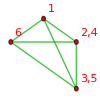
-Graphics-{7181095→v1x24x35x6,1}Missing[KeyAbsent,compwhy]

```mathematica
CosyPrint6[InverseKey6[v1x24x35x6],stubbornForm6]
```

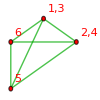
```mathematica
-Graphics-{8775337->v13x24x5x6,1}Missing["KeyAbsent","compwhy"];
```

```mathematica
MyPlanar[stubbornForm6,InverseKey6[v13x24x5x6]]
```

False

```mathematica
Clear[sol]
```

```mathematica
Reduce[fiveequalssix&&v13x24x5x6+v14x2x35x6+v1x24x35x6==0&&v16x24x35==0&&v1x24x35x6==0&&v14x2x35x6==0&&0==v16x24x35+v16x24x3x5+v16x2x35x4&&v1x2x35x4==0&&v16x24x3x5==0&&v13x24x5x6+v13x2x4x5x6+v14x2x35x6+v14x2x3x5x6+v16x24x35+v16x24x3x5+v16x2x35x4+v16x2x3x4x5+v1x24x35x6+v1x24x3x5x6+v1x2x35x4x6+v1x2x3x4x5x6>0,sol]/.repcolofour5base/.repcolofour6base
```

False

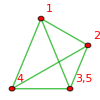
-Graphics-{29527→v1x2x35x4,1}No IH

```mathematica
CosyPrint5[InverseKey[v1x2x35x4]]
```

```mathematica
CosyPrint5[InverseKey[v1x2x35x4]]
```

```mathematica
MyPlanar[stubbornForm6,InverseKey6[v1x24x35x6]]
```

False

```mathematica
CosyPrint6[InverseKey6[v1x24x35x6]]
```

-Graphics-{7181095→v1x24x35x6,1}

```mathematica
(Reduce[fiveequalssix])/.repcolofour5base/.repcolofour6base
```

-Graphics-v16x2x35x4==-Graphics-v1x2x35x4&&-Graphics-v16x24x3x5==-Graphics-v1x24x3x5&&-Graphics-v16x24x35==2 -Graphics-v1x24x35--Graphics-v1x24x35x6&&-Graphics-v14x2x35==-Graphics-v14x2x35x6&&-Graphics-v13x2x4x5x6==--Graphics-v1x24x3x5x6--Graphics-v1x2x35x4x6--Graphics-v14x2x3x5x6--Graphics-v16x2x3x4x5--Graphics-v1x2x3x4x5x6&&-Graphics-v13x24x5x6==--Graphics-v1x24x35x6--Graphics-v14x2x35x6&&-Graphics-v13x24x5==--Graphics-v1x24x35x6--Graphics-v14x2x35x6

```mathematica
stubbornForm6[4982998]["colofour"]
```

v13x24x5x6+v13x2x4x5x6+v14x2x35x6+v14x2x3x5x6+v16x24x35+v16x24x3x5+v16x2x35x4+v16x2x3x4x5+v1x24x35x6+v1x24x3x5x6+v1x2x35x4x6+v1x2x3x4x5x6

```mathematica
ineqsthree62=Fold[And,ineqsthree6];
```

$Aborted

```mathematica
Length[ineqsthree6]
```

53071